-Graphics-

# Social Networks Derived From Narrative Texts

-Graphics-

## Introduction

### Disclaimer

The data and analysis reported here were recently published, and are in no way the original work of today’s speaker.

The publication is

Network analysis of the Viking Age in Ireland as portrayed in Cogadh Gaedhel re Gallaibh
Joseph Yose, Ralph Kenna, Máirín MacCarron, Pádraig MacCarron
R. Soc. open sci. 2018 5 171024; DOI: 10.1098/rsos.171024. Published 24 January 2018

References in the following slides (e.g., [6]) are to those in the original publication.

Today’s speaker is actively working with the authors to make the data and analysis available in the Wolfram Data Repository.

### Background

The Battle of Clontarf (1014), an iconic event in the history of Ireland, is traditionally remembered as marking the decline of Viking power after some two centuries in the country.

For the past 250 years, a debate has been taking place centred around what may be called ‘traditionalist’ and ‘revisionist’ views of the period [2–7].

The recent millennial anniversary of the battle inspired academics to revisit the debate through new journal papers, books, booklets, monographs, online commentaries and media engagements (e.g. [7–18]).

As with earlier investigations, these approaches treat the subject matter using traditional tools of the humanities (e.g. [19–48]).

Here, the authors present an alternative, complexity science-based investigation, using one of the most famous accounts of the Vikings in Ireland: Cogadh Gaedhel re Gallaibh ('The war of the Gaedhil with the Gaill' or 'War of the Irish with the Foreigners').

The events associated with the Viking Age in Ireland and Battle of Clontarf are nowadays frequently considered as having entered the public imagination in an overly simplified manner.

That popular picture is essentially of an 'international' conflict—Irish versus Viking—in which victory for the former ended the latter's ambitions in the country.

The truth, we are told, is more nuanced and more complex [5,6].

Instead of an international conflict, the issue at stake at Clontarf was an internal, domestic, Irish struggle: the determination of Leinster (in the east of Ireland) to remain independent of the dominant dynasties to its north and south-west [5,6].

Some such interpretations, wherein the Vikings are said to have played a secondary role, tend to downplay the significance of Clontarf [16] and have been partly ascribed to revisionist fashions [7,36].

Cogadh Gaedhel re Gallaibh has been used to bolster arguments on both sides of the debate.

The authors’ aim is to determine what character networks in the CGG have to say on the matter.

It is important to state from the outset that this analysis is of the content of Cogadh Gaedhel re Gallaibh and its portrayal of the Viking Age in Ireland.

We do not have direct access to the actual social networks of the period and we recognize that the account in the Cogadh has been influenced by events and circumstances after 1014 and up to the composition of the text.

## Rationale

We are interested in the question whether the Cogadh networks are consistent with the traditional depiction of a contest which is clear-cut international or if they support the revisionist notion of a power-struggle which is mostly domestic or, indeed, if they deliver something between both pictures.

The entire set of interacting characters in Cogadh Gaedhel re Gallaibh and the relationships between them is represented in the figure, and represents a network of considerable complexity, similar to those of other epic narratives

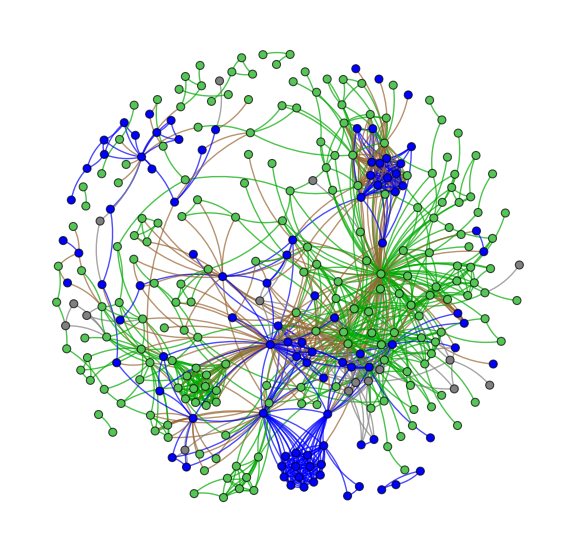

A simple tally of edges (interactions between characters) will not do as this would not account for different numbers of Irish and Viking nodes, and a proper quantitative approach instead necessitates the networks-science concepts of assortativity and disassortativity.

## Methodology

The approach used to construct the networks followed the methodology of [49–51] in that nodes and links are identified by carefully and manually reading the texts with multiple passes through all of the material by multiple readers.

In the authors’ experience, such an approach is required to minimize errors and omissions as well as to reduce levels of subjectivity.

Cogadh Gaedhel re Gallaibh is a very dense text and meticulous care is required to interpret extremely subtle tracts containing large amounts of explicit and implicit information.

It is currently beyond technological capabilities to extract such information automatically owing to the inherent complexity of such texts (see, e.g. [62]).

Establishing the technology for such an approach is another active area of research.

## Data

The raw data are available at Github: https://github.com/ralphkenna/CGG

We imported them and prepared a Wolfram Data Repository object

```mathematica
$$Object["FullContent"]=DataResource`$$ContentConversion@
<|
"CogadhGaedhelGallaibhNetworks"->CloudObject[["https://www.wolframcloud.com/objects/rnachbar/CGG-WDX"](https://www.wolframcloud.com/objects/rnachbar/CGG-WDX)]
|>;
```

```mathematica
data=$$Object["FullContent"]["CogadhGaedhelGallaibhNetworks"];
```

```mathematica
Keys@data
```

{Characters,FullNetwork,PositiveNetwork,NegativeNetwork}

### Characters

The character data consists of the character’s name and nationality, as a Dataset

```mathematica
data["Characters"]
```

Dataset[<>]

### Networks

There are 3 main networks

The full network without regard to the nature of the characters’ interaction (sentiment)

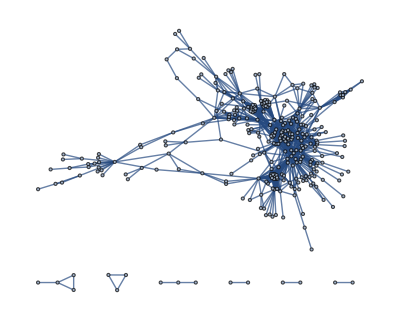

```mathematica
data["FullNetwork"]
```

The network of positive, or friendly, interactions

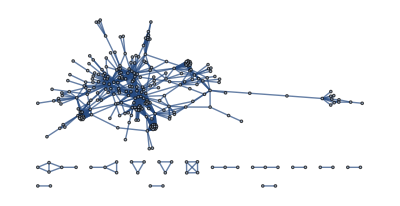

```mathematica
data["PositiveNetwork"]
```

The network of negative, or hostile, interactions

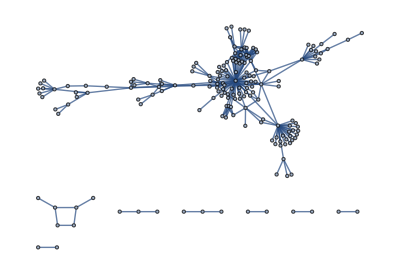

```mathematica
data["NegativeNetwork"]
```

## Character nationalities

We defined some predicates (see Initialization slide) to facilitate the analysis

```mathematica
?faction
```

faction[character] returns the nationality ("Irish", "Viking", or "Other" of character.

```mathematica
?irishQ
```

irishQ[character] returns True if character is "Irish" and False otherwise.

```mathematica
?vikingQ
```

vikingQ[character] returns True if character is "Viking" and False otherwise.

```mathematica
?otherQ
```

otherQ[character] returns True if character is "Unassigned" and False otherwise.

Here is a sample of the character data

```mathematica
With[{characters={"Baetan","Snuatgar","Gaithin","Macbeth"}},{faction[#],irishQ[#],vikingQ[#],otherQ[#]}&@characters//Transpose//TableForm[#,TableHeadings->{characters,{"Faction","Irish?","Viking?","Other?"}}]&]
```

| Faction | Irish? | Viking? | Other?
Baetan | Irish | True | False | False
Snuatgar | Viking | False | True | False
Gaithin | Unassigned | False | False | True
Macbeth | Missing[NotAvailable] | False | False | False

## The character networks

### Interaction (edge) sentiment

We distinguish between two types of edge: positive and negative.

Positive edges are established when any two characters are related, communicate directly with each another, or speak about one another, or are present together when it is clear that they know each other.

So positive edges ordinarily represent familial or social relationships.

Negative links, on the other hand, are formed when two characters meet in physical conflict or when animosity is explicitly declared by one character against another and it is clear they know each other (such as a declaration of war).

So negative edges typically represent actual or intended physical hostility.

It is possible that two characters are linked by both positive and negative edges as relationships between characters may change over time.

### Signed, national networks

We next created network Graph objects for the full cast, Irish, and Viking networks.

```mathematica
ClearAll[network]
network::usage="network[sign, faction] returns a Graph object of the characters belonging to faction whose interactions are of type sign.";
Do[
Module[{edges,vertices},edges=Cases[s⟦2⟧,_?(n⟦2⟧)<->_?(n⟦2⟧)];vertices=Union@@List@@@edges;network[s⟦1⟧,n⟦1⟧]=Graph[vertices,edges]],{s,{{"Unsigned",EdgeList@data["FullNetwork"]},{"Positive",EdgeList@data["PositiveNetwork"]},{"Negative",EdgeList@data["NegativeNetwork"]}}},{n,{{"FullCast",True&},{"Irish",irishQ},{"Viking",vikingQ}}}]
```

```mathematica
(First/@DownValues[network])/.HoldPattern->HoldForm//Column
```

network[Negative,FullCast]
network[Negative,Irish]
network[Negative,Viking]
network[Positive,FullCast]
network[Positive,Irish]
network[Positive,Viking]
network[Unsigned,FullCast]
network[Unsigned,Irish]
network[Unsigned,Viking]

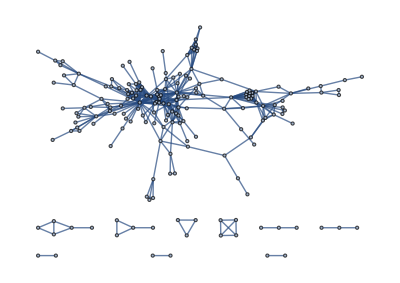

```mathematica
network["Positive","Irish"]
```

### Overview of the networks

We want some useful lists for constructing networks and tables

```mathematica
edgeTypes={"Unsigned","Positive","Negative"};
```

```mathematica
factions={"FullCast","Irish","Viking"};
```

We used a novel embedding method for the vertex layout

```mathematica
?gravityEmbedding
```

gravityEmbedding[g] returns the Graph g with the vertices laid out using the so-called "gravity" embedding.

```mathematica
TabView[Function[edgeType,edgeType->Module[{g=network[edgeType,"FullCast"],vertexStyles,edgeStyles},vertexStyles=#->Switch[faction[#],"Irish",Lighter@Darker@Green,"Viking",Blue,_(*"Unassigned"*),Gray]&/@VertexList[g];
edgeStyles=#->Switch[faction[#],"Irish"<->"Irish",Darker@Green,"Viking"<->"Viking",Blue,("Irish"<->"Viking")|("Viking"<->"Irish"),Brown,_(*"Unassigned"*),Gray]&/@EdgeList[g];
gravityEmbedding[g,VertexStyle->vertexStyles,VertexLabels->Placed["Name",Tooltip],EdgeStyle->edgeStyles,EdgeShapeFunction->"CurvedArc",ImageSize->Large]
]]/@edgeTypes]
closeInputCell[]
```

123

Null^3

Green vertices are Irish characters, blue vertices are Viking characters, and gray vertices are Unassigned vertices

Green edges are between two Irish characters, blue edges are between two Viking characters, and brown edges are between two Unassigned characters or between mixed pairs of characters

## Structural network statistics

### Vertex and edge counts

```mathematica
Outer[{#1,#2,VertexCount@network[##],EdgeCount@network[##]}&,edgeTypes,factions]//Flatten[#,1]&//Grid[Prepend[#,{"relationship","faction","N","M"}],Alignment->{{Left,Left,{Decimal}}},Spacings->{2,Automatic},Dividers->{None,{False,True,{False,False,Gray},False}},Background->{None,{None,Sequence@@ConstantArray[None,3],Sequence@@ConstantArray[LightBlue,3],Sequence@@ConstantArray[LightPink,3]}}]&//Labeled[#,Style["Vertex and edge counts",Bold],Top]&
closeInputCell[]
```

relationship | faction | N | M
Unsigned | FullCast | 315 | 1190
Unsigned | Irish | 193 | 530
Unsigned | Viking | 91 | 313
Positive | FullCast | 287 | 957
Positive | Irish | 186 | 475
Positive | Viking | 88 | 301
Negative | FullCast | 180 | 264
Negative | Irish | 62 | 72
Negative | Viking | 18 | 16Vertex and edge counts

Null^3

The unsigned network has 315 individual interacting characters connected by 1190 edges

The signed, that is, friendly (positive) and hostile (negative), networks are somewhat smaller

These are the networks that allows one to gain more insight into the social and conflictual statistics contained in the narrative

### Vertex degree

The number of edges touching a vertex is the same as the number of social interactions the corresponding character has with other characters

#### Average vertex degree

```mathematica
makeTable[N@((2EdgeCount[#])/VertexCount[#])&,edgeTypes,factions,"Average vertex degree ⟨k⟩"]
```

| FullCast | Irish | Viking
Unsigned | 7.55556 | 5.49223 | 6.87912
Positive | 6.66899 | 5.10753 | 6.84091
Negative | 2.93333 | 2.32258 | 1.77778Average vertex degree ⟨k⟩

The average number of edges per node for the entire network is ⟨k⟩ = 2M/N ≈ 7.6

#### Maximum vertex degree

```mathematica
makeTable[Max@VertexDegree[#]&,edgeTypes,factions,"Maximum vertex degree k_max"]
```

| FullCast | Irish | Viking
Unsigned | 105 | 63 | 26
Positive | 53 | 47 | 26
Negative | 63 | 25 | 4Maximum vertex degree k_max

For the entire network, the most connected character is Brian Boru

k_max = 105 edges

That is, he is linked to 33% of the other characters in the narrative

#### Degree assortativity

Sociology has shown that societies exhibit homophily, the tendency of individuals to associate with others who are similar to themselves

In the field of social network analysis, this is known as assortativity.

Degree assortativity is the extent to which nodes of similar degree tend to link up.

Studies of other epic literature has identified the tendency of nodes to attach to other nodes with similar numbers of links.

Positive (friendly) sub-networks tend to exhibit degree assortativity, or they are uncorrelated

Negative sub-networkstend to be just the opposite, showing degree disassortativity

```mathematica
makeTable[N@GraphAssortativity[#]&,edgeTypes,factions,"Degree assortativity r"]
```

| FullCast | Irish | Viking
Unsigned | -0.0860726 | -0.084198 | 0.304766
Positive | -0.00300764 | -0.0206245 | 0.337237
Negative | -0.253901 | -0.260154 | -0.0764526Degree assortativity r

In the CGG, as with other character networks, the negative full-cast network is disassortative by degree r = −0.25

This means that high-degree characters are hubs and their negative links preferentially attach to low-degree ones

This appears to be a generic feature of heroic tales in particular, where the hero or heroes encounter multitudes of lesser characters and defeat them in battle

The positive full-cast network is uncorrelated (r = −0.003), meaning it is neither assortative nor disassortative.

These features are typical of social networks and of character networks with positive interactions

## Semantic network statistics

### Identity profiles

The proportions of Irish, Viking and other nodes in the unsigned networks, and in the positive and negative sub-networks, are shown in the table

```mathematica
Outer[#1[#2]&,{With[{n=Count[VertexList[network[#,"FullCast"]],_?irishQ]},{n,100N[n/VertexCount[network[#,"FullCast"]]]}]&,With[{n=Count[VertexList[network[#,"FullCast"]],_?vikingQ]},{n,100N[n/VertexCount[network[#,"FullCast"]]]}]&,With[{n=Count[VertexList[network[#,"FullCast"]],_?otherQ]},{n,100N[n/VertexCount[network[#,"FullCast"]]]}]&,With[{n=Count[VertexList[network[#,"FullCast"]],_]},{n,100N[n/VertexCount[network[#,"FullCast"]]]}]&,With[{n=Count[Map[nationality,EdgeList[network[#,"FullCast"]],{2}],"Irish"<->"Irish"]},{n,100N[n/EdgeCount[network[#,"FullCast"]]]}]&,With[{n=Count[Map[nationality,EdgeList[network[#,"FullCast"]],{2}],"Viking"<->"Viking"]},{n,100N[n/EdgeCount[network[#,"FullCast"]]]}]&,With[{n=Count[Map[nationality,EdgeList[network[#,"FullCast"]],{2}],"Irish"<->"Viking"|"Viking"<->"Irish"]},{n,100N[n/EdgeCount[network[#,"FullCast"]]]}]&,With[{n=Count[Map[nationality,EdgeList[network[#,"FullCast"]],{2}],_]},{n,100N[n/EdgeCount[network[#,"FullCast"]]]}]&},edgeTypes]//Apply[StringForm["`` (``%}",#1,Round[#2]]&,#,{2}]&//MapThread[Prepend,{#,{"Irish nodes","Viking nodes","Other nodes","Total # nodes","Irish-Irish edges","Viking-Viking edges","Irish-Viking edges","Total # edges"}}]&//Prepend[#,Prepend[edgeTypes,""]]&//Grid[#,Dividers->{{False,True,False},{False,{True,False,False,Gray},False}},Alignment->{{Left,{"("}},Automatic,{{1,2}->"g",{1,3}->"t",{1,4}->"t"}},Spacings->{{1,{2}},Automatic}]&
closeInputCell[]
```

| Unsigned | Positive | Negative
Irish nodes | 202 (64%} | 187 (65%} | 110 (61%}
Viking nodes | 97 (31%} | 88 (31%} | 61 (34%}
Other nodes | 16 (5%} | 12 (4%} | 9 (5%}
Total # nodes | 315 (100%} | 287 (100%} | 180 (100%}
Irish-Irish edges | 0 (0%} | 0 (0%} | 0 (0%}
Viking-Viking edges | 0 (0%} | 0 (0%} | 0 (0%}
Irish-Viking edges | 0 (0%} | 0 (0%} | 0 (0%}
Total # edges | 1190 (100%} | 957 (100%} | 264 (100%}

Null^3

The proportions of Irish nodes in each of the three graphs are approximately constant at 61%–65 %

The proportion of Viking nodes is also relatively stable between 31% and 34%.

In the positive network:

50% of edges in the positive network link pairs of Irish nodes

31% connect pairs of Viking nodes

12% of positive interactions connect mixed Irish– Viking pairs.

In the negative network:

27% of links connect Irish to Irish nodes

6% connect pairs of Viking nodes

over 62% of negative interactions connect mixed Irish–Viking pairs

In other words, the positive (social) network is dominated by interactions between characters of the same narrative identities (intranational interactions) and the negative (conflictual) network is dominated by Irish–Viking (international) interactions.

This suggests that the largest proportion of Cogadh conflict is international, but there are significant levels of intranational hostilities too (especially Irish versus Irish).

### Categorical assortativity

To properly evaluate the levels of mixing, negative or positive, between Irish and Viking, one must take into account factional to which each character belongs

This can be assesses with the categorical assortativity of the various networks, represented ρ

It is a measure which ranges between ρ_min and 1, where ρ_min is a non-trivial, negative value, which itself lies between −1 and 0 if there are more than two categories under consideration, and is therefore network dependent

When there are more than two categories, disassortativity connects dissimilar nodes, just as randomness does

Assortativity, however, connects like nodes and is therefore quite different from randomness.

The only instance in which ρ_min = −1 is when there are two categories.

The value ρ = 1 indicates 100% categorical assortativity

If this were the case for our positive network, it would mean that positive interactions occur only within categories; that is, friendly interactions would be intranational

The value ρ = ρ_min < 0 implies that the network is fully categorically disassortative

This situation implies that positive interactions would be international

A value ρ = 0 would indicate that the categorical assortativity is the same as would be expected for random mixing between nodes, oblivious of their Irish or Viking character

```mathematica
makeTable[With[{nodes=VertexList[#]},N@GraphAssortativity[#,nodes->faction[nodes]]]&,edgeTypes,factions,"Categorical assortativity ρ"]
```

| FullCast | Irish | Viking
Unsigned | 0.451986 | 0. | 0.
Positive | 0.65216 | 0. | 0.
Negative | -0.315864 | 0. | 0.Categorical assortativity ρ

The full-cast positive network has a large positive categorical assortativity of 0.65

This suggests that most (but not all) friendly interactions are between the same factions.

The full-cast negative network has a moderate negative categorical assortativity of -0.32

This suggests that hostile interactions tend to be between the different factions.

The Cogadh Gaedhel re Gallaibh is a narrative that presents the highest level of conflict between Irish and Viking, but with significant amounts of Irish-on-Irish and Viking-on-Viking conflict also.

## Network robustness

### Character importance

Besides Brian's vertex degree, we are also interested in the connectedness of other characters and we rank the first few characters according to their individual degrees, and according to other measures of importance

We use various vertex centrality measures available in WL

#### Betweenness centrality

BetweennessCentrality will give high centralities to vertices that are on many shortest paths of other vertex pairs

We used a normalized betweenness centrality

```mathematica
betweennessCentrality[g_Graph]/;VertexCount[g]>2:=(2BetweennessCentrality[g])/((VertexCount[g]-1)(VertexCount[g]-2))
betweennessCentrality[g_Graph]:=ConstantArray[0.,VertexCount[g]]
```

#### Closeness centrality

ClosenessCentrality will give high centralities to vertices that are at a short average distance to every other reachable vertex

The closeness centrality of a node is relevant only if the vertex is a member of the giant component.

```mathematica
closenessCentrality[g_Graph]:=With[{bigComponent=First@ConnectedComponents[g]},MapThread[If[MemberQ[bigComponent,#1],#2,0]&,{VertexList[g],ClosenessCentrality[g]}]]
```

#### Katz centrality

KatzCentrality will give high centralities to vertices that exhibit a high degree of influence within a network by measuring the number of the immediate neighbors (first degree nodes) and also all other nodes in the network that connect to the node under consideration through these immediate neighbors

Katz centrality can also be used in estimating the relative status or influence of actors in a social network

The Katz centrality requires an attenuation factor, which we will determine empirically from the data

```mathematica
katzCentrality[g_Graph]:=With[{α=Max[Abs[EigenvectorCentrality[g]]]},KatzCentrality[g,α]]
```

#### The important characters of each network

```mathematica
centralities={DegreeCentrality,betweennessCentrality,closenessCentrality,katzCentrality};
```

```mathematica
Outer[Function[{et,cent},With[{g=network[et,"FullCast"]},Take[#,5]&@Reverse@SortBy[Thread[{VertexList[g],cent[g]}],Last]]],edgeTypes,centralities]/.{char_String,cen_?NumberQ}:>(Style[#,12]&@StringForm["`` (``)",char,Switch[cen,_Integer,cen,_,PaddedForm[Round[cen,0.01],{3,2},NumberSigns->{"",""}]]])//Map[Column,#,{2}]&//TableForm[#,TableHeadings->{edgeTypes,centralities},TableSpacing->{4,2}]&//Labeled[#,Style["Character importance",Bold],Top]&
closeInputCell[]
```

| DegreeCentrality | betweennessCentrality | closenessCentrality | katzCentrality
Unsigned | Brian Boru (105)
Sitriuc the blind (62)
Maelmordha son of Murchadh (42)
Earl Ottir (40)
Maelsechlainn (Malachy 11) (36) | Brian Boru (0.42)
Sitriuc the blind (0.21)
Earl Ottir (0.16)
Aedh Finnliath (0.13)
Ossill (0.11) | Brian Boru (0.46)
Sitriuc the blind (0.43)
Earl Ottir (0.41)
Gormflaith (0.40)
Maelmordha son of Murchadh (0.40) | Brian Boru (11.70)
Sitriuc the blind (7.62)
Maelmordha son of Murchadh (6.04)
Gormflaith (5.57)
Earl Ottir (5.38)
Positive | Brian Boru (53)
Sitriuc the blind (40)
Maelmordha son of Murchadh (38)
Gormflaith (34)
Earl Ottir (32) | Brian Boru (0.28)
Sitriuc the blind (0.17)
Maelsechlainn (Malachy 11) (0.11)
Earl Ottir (0.10)
Gormflaith (0.10) | Sitriuc the blind (0.39)
Brian Boru (0.39)
Gormflaith (0.39)
Maelmordha son of Murchadh (0.37)
Maelsechlainn (Malachy 11) (0.36) | Brian Boru (3.84)
Sitriuc the blind (3.58)
Maelmordha son of Murchadh (3.50)
Gormflaith (3.36)
Earl Ottir (3.23)
Negative | Brian Boru (63)
Sitriuc the blind (25)
Mathgamhain (17)
Cathal Son of Feradach (14)
Olaf Cuaran (12) | Brian Boru (0.63)
Earl Ottir (0.23)
Sitriuc the blind (0.23)
Aedh Finnliath (0.16)
Olaf Cuaran (0.12) | Brian Boru (0.49)
Maelsechlainn (Malachy 11) (0.40)
Sitriuc the blind (0.39)
Earl Ottir (0.38)
Ivar grandson of Ivar (0.36) | Brian Boru (10.30)
Sitriuc the blind (4.13)
Mathgamhain (3.82)
Cathal Son of Feradach (3.55)
Maelsechlainn (Malachy 11) (3.37)Character importance

Null^3

### Stability of the giant component

From the network drawings shown earlier, we see that they are only a few isolated vertices or disconnected components, leaving most of the vertices in what is commonly called the giant component

One method to assess the stability of the giant component remove one node at time and records the size of the giant component in the resulting subgraph

The removal of nodes can be random or based on node importance

If a network has a few highly important nodes, then removing them first will tend to destroy the giant component fairly quickly when compared to removing nodes randomly

We used 5 trials for random removal

```mathematica
giantComponentSize[g_Graph]:=With[{cc=ConnectedComponents[g]},Switch[cc,{__},Length@First@cc,_,0]]
```

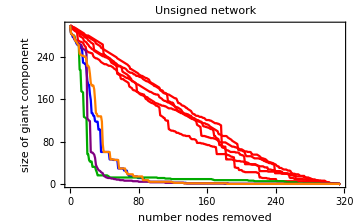
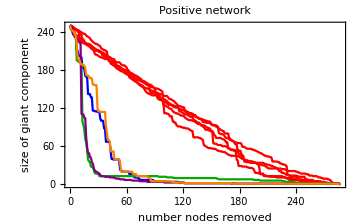
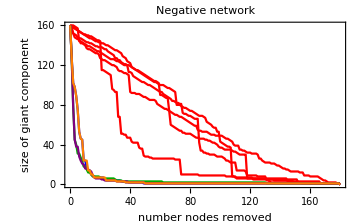
-Graphics- | -Graphics-
-Graphics- |

Null^3

```mathematica
Module[{random,degree,betweenness,closeness,katz},random=Table[giantComponentSize/@With[{g=network[#,"FullCast"]},NestList[VertexDelete[#,RandomSample[VertexList[#],1]]&,g,VertexCount[g]]],{5}]&/@edgeTypes;
degree=giantComponentSize/@With[{g=network[#,"FullCast"]},NestList[VertexDelete[#,Last@Last@Sort@Thread[{DegreeCentrality[#],VertexList[#]}]]&,g,VertexCount[g]]]&/@edgeTypes;
betweenness=giantComponentSize/@With[{g=network[#,"FullCast"]},NestList[VertexDelete[#,Last@Last@Sort@Thread[{betweennessCentrality[#],VertexList[#]}]]&,g,VertexCount[g]]]&/@edgeTypes;
closeness=giantComponentSize/@With[{g=network[#,"FullCast"]},NestList[VertexDelete[#,Last@Last@Sort@Thread[{closenessCentrality[#],VertexList[#]}]]&,g,VertexCount[g]]]&/@edgeTypes;
katz=giantComponentSize/@With[{g=network[#,"FullCast"]},NestList[VertexDelete[#,Last@Last@Sort@Thread[{katzCentrality[#],VertexList[#]}]]&,g,VertexCount[g]]]&/@edgeTypes;
MapThread[Function[{r,d,b,c,k,e},ListPlot[Thread[{Range[0,VertexCount[network[e,"FullCast"]]],#}]&/@Join[r,{d,b,c,k}],Joined->True,PlotMarkers->None,PlotLabel->StringForm["`` network",e],FrameLabel->{"number nodes removed","size of giant component"},PlotStyle->Join[ConstantArray[Red,Length@r],{Blue,Darker@Green,Purple,Orange}],ImageSize->Medium]],{random,degree,betweenness,closeness,katz,edgeTypes}]//Append[#,Framed@LineLegend[{Red,Blue,Darker@Green,Purple,Orange},{"random","by decreasing degree centrality","by decreasing betweenness centrality","by decreasing closeness centrality","by decreasing Katz centrality"},LegendLabel->"node removal order"]]&//Partition[#,2,2,{1,1},{""}]&//Grid
]
closeInputCell[]
```

This analysis shows that the networks are dominated by a few highly connected characters, and is consistent with the degree assortativity analysis above

## Conclusions

The categorical assortativity for the conflictual network is moderately negative, indicating that the hostilities were mostly between the Irish and the Vikings.

While the Cogadh account is not as clear cut as either the most traditional or revisionist pictures in the debate depict, it lies on the traditional side.

The networks of Cogadh Gaedhel re Gallaibh present a complex social structure of the Viking Age in Ireland comprising predominantly international conflict, but with strong degrees of intranational hostilities also.

## Initialization

```mathematica
ClearAll[faction]
faction::usage="faction[character] returns the nationality (\"Irish\", \"Viking\", or \"Other\" of character.";
SetAttributes[faction,Listable];
Scan[(faction[#["Character"]]=#["Faction"])&,data["Characters"]]
faction[e:(_DirectedEdge|_UndirectedEdge)]:=faction/@e
faction[_]:=Missing["NotAvailable"]
```

```mathematica
ClearAll[irishQ]
irishQ::usage="irishQ[character] returns True if character is \"Irish\" and False otherwise.";
SetAttributes[irishQ,Listable];
Scan[(irishQ[#["Character"]]=MatchQ[#["Faction"],"Irish"])&,data["Characters"]]
irishQ[_]:=False
```

```mathematica
ClearAll[vikingQ]
vikingQ::usage="vikingQ[character] returns True if character is \"Viking\" and False otherwise.";
SetAttributes[vikingQ,Listable];
Scan[(vikingQ[#["Character"]]=MatchQ[#["Faction"],"Viking"])&,data["Characters"]]
vikingQ[_]:=False
```

```mathematica
ClearAll[otherQ]
otherQ::usage="otherQ[character] returns True if character is \"Unassigned\" and False otherwise.";
SetAttributes[otherQ,Listable];
Scan[(otherQ[#["Character"]]=MatchQ[#["Faction"],"Unassigned"])&,data["Characters"]]
otherQ[_]:=False
```

```mathematica
gravityEmbedding::usage="gravityEmbedding[g] returns the Graph g with the vertices laid out using the so-called \"gravity\" embedding.";
gravityEmbedding[g_Graph,opts:OptionsPattern[{Graph}]]:=Module[{newVertex=Unique[v],newEdges,coords,gOpts},newEdges=(newVertex<->#1&)/@VertexList[g];coords=GraphEmbedding[EdgeAdd[VertexAdd[g,newVertex],newEdges],"SpringElectricalEmbedding",2];gOpts=FilterRules[Options[g],Except[{VertexCoordinates,GraphLayout}]];Graph[VertexList[g],EdgeList[g],VertexCoordinates->Most[coords],opts,gOpts]]
```

```mathematica
closeInputCell[]:=(
SelectionMove[EvaluationCell[],Before,Cell(*,AutoScroll->False*)]
SelectionMove[EvaluationCell[],Next,Cell(*,AutoScroll->False*)]
FrontEndTokenExecute[EvaluationNotebook[],"OpenCloseGroup"]
)
```

```mathematica
makeTable[f_,rows_,columns_,title_]:=Outer[f[network[##]]&,rows,columns]//TableForm[#,TableHeadings->{rows,columns}]&//Labeled[#,Style[title,Bold],Top]&
```